```mathematica
Bisection[f_,a0_,b0_,xtol_,ytol_,nmax_]:=
Module[{a,b,fa,fb,c,fc,p},
a=a0;
b=b0;
fa=f[a];
fb=f[b];
If[Sign[fa]*Sign[fb]>0,{a,-1}];
c=(a+b)/2.0;
fc=2*ytol;
p=1;
While[(Abs[b-a]>xtol*2)&&(Abs[fc]>ytol)&&(p<nmax),
c=(a+b)/2.0;fc=f[c];
If[Sign[fa]*Sign[fc]<0,b=c; fb=fc;
c=(a+b)/2.0;fc=f[c];p+=1,
a=c;fa=fc;c=(a+b)/2.0;fc=f[c];
p+=1;]];
{c,p}]
```

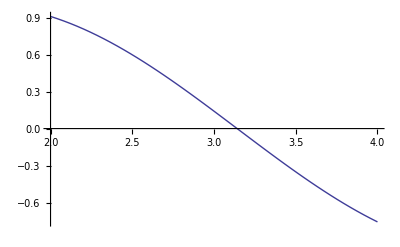

{3.14159,21}

```mathematica
f1[x_]:=Sin[x];Plot[f1[x],{x,2,4}]
Bisection[f1,2,4,10^-6,10^-7,50]
```